# 2.2 Damped pendulum

```mathematica
σ = 1
```

1

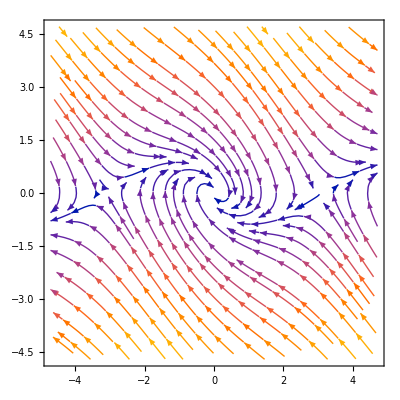

```mathematica
StreamPlot[{y, -Sin[x]-σ*y}, {x,-1.5*π,1.5*π}, {y,-1.5*π,1.5*π}]
```

```mathematica
minx = -1.5*π;
miny = -1.5*π;
maxx = 1.5*π;
maxy = 1.5*π;
```

```mathematica
sol[x0_ , y0_] :=NDSolve[
{x'[t]== y [t], 
y'[t] == -Sin[x[t]]-σ *y[t], x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,10}]
```

```mathematica
dz = 0.5
```

0.5

```mathematica
z = 4
```

4

```mathematica
initialC=Tuples[{Range[-z,z,dz],Range[-z,z,dz]}]
```

{{-4.,-4.},{-4.,-3.5},{-4.,-3.},{-4.,-2.5},{-4.,-2.},{-4.,-1.5},{-4.,-1.},{-4.,-0.5},{-4.,0.},{-4.,0.5},{-4.,1.},{-4.,1.5},{-4.,2.},{-4.,2.5},{-4.,3.},{-4.,3.5},{-4.,4.},{-3.5,-4.},{-3.5,-3.5},{-3.5,-3.},{-3.5,-2.5},{-3.5,-2.},{-3.5,-1.5},{-3.5,-1.},{-3.5,-0.5},{-3.5,0.},{-3.5,0.5},{-3.5,1.},{-3.5,1.5},{-3.5,2.},{-3.5,2.5},{-3.5,3.},{-3.5,3.5},{-3.5,4.},{-3.,-4.},{-3.,-3.5},{-3.,-3.},{-3.,-2.5},{-3.,-2.},{-3.,-1.5},{-3.,-1.},{-3.,-0.5},{-3.,0.},{-3.,0.5},{-3.,1.},{-3.,1.5},{-3.,2.},{-3.,2.5},{-3.,3.},{-3.,3.5},{-3.,4.},{-2.5,-4.},{-2.5,-3.5},{-2.5,-3.},{-2.5,-2.5},{-2.5,-2.},{-2.5,-1.5},{-2.5,-1.},{-2.5,-0.5},{-2.5,0.},{-2.5,0.5},{-2.5,1.},{-2.5,1.5},{-2.5,2.},{-2.5,2.5},{-2.5,3.},{-2.5,3.5},{-2.5,4.},{-2.,-4.},{-2.,-3.5},{-2.,-3.},{-2.,-2.5},{-2.,-2.},{-2.,-1.5},{-2.,-1.},{-2.,-0.5},{-2.,0.},{-2.,0.5},{-2.,1.},{-2.,1.5},{-2.,2.},{-2.,2.5},{-2.,3.},{-2.,3.5},{-2.,4.},{-1.5,-4.},{-1.5,-3.5},{-1.5,-3.},{-1.5,-2.5},{-1.5,-2.},{-1.5,-1.5},{-1.5,-1.},{-1.5,-0.5},{-1.5,0.},{-1.5,0.5},{-1.5,1.},{-1.5,1.5},{-1.5,2.},{-1.5,2.5},{-1.5,3.},{-1.5,3.5},{-1.5,4.},{-1.,-4.},{-1.,-3.5},{-1.,-3.},{-1.,-2.5},{-1.,-2.},{-1.,-1.5},{-1.,-1.},{-1.,-0.5},{-1.,0.},{-1.,0.5},{-1.,1.},{-1.,1.5},{-1.,2.},{-1.,2.5},{-1.,3.},{-1.,3.5},{-1.,4.},{-0.5,-4.},{-0.5,-3.5},{-0.5,-3.},{-0.5,-2.5},{-0.5,-2.},{-0.5,-1.5},{-0.5,-1.},{-0.5,-0.5},{-0.5,0.},{-0.5,0.5},{-0.5,1.},{-0.5,1.5},{-0.5,2.},{-0.5,2.5},{-0.5,3.},{-0.5,3.5},{-0.5,4.},{0.,-4.},{0.,-3.5},{0.,-3.},{0.,-2.5},{0.,-2.},{0.,-1.5},{0.,-1.},{0.,-0.5},{0.,0.},{0.,0.5},{0.,1.},{0.,1.5},{0.,2.},{0.,2.5},{0.,3.},{0.,3.5},{0.,4.},{0.5,-4.},{0.5,-3.5},{0.5,-3.},{0.5,-2.5},{0.5,-2.},{0.5,-1.5},{0.5,-1.},{0.5,-0.5},{0.5,0.},{0.5,0.5},{0.5,1.},{0.5,1.5},{0.5,2.},{0.5,2.5},{0.5,3.},{0.5,3.5},{0.5,4.},{1.,-4.},{1.,-3.5},{1.,-3.},{1.,-2.5},{1.,-2.},{1.,-1.5},{1.,-1.},{1.,-0.5},{1.,0.},{1.,0.5},{1.,1.},{1.,1.5},{1.,2.},{1.,2.5},{1.,3.},{1.,3.5},{1.,4.},{1.5,-4.},{1.5,-3.5},{1.5,-3.},{1.5,-2.5},{1.5,-2.},{1.5,-1.5},{1.5,-1.},{1.5,-0.5},{1.5,0.},{1.5,0.5},{1.5,1.},{1.5,1.5},{1.5,2.},{1.5,2.5},{1.5,3.},{1.5,3.5},{1.5,4.},{2.,-4.},{2.,-3.5},{2.,-3.},{2.,-2.5},{2.,-2.},{2.,-1.5},{2.,-1.},{2.,-0.5},{2.,0.},{2.,0.5},{2.,1.},{2.,1.5},{2.,2.},{2.,2.5},{2.,3.},{2.,3.5},{2.,4.},{2.5,-4.},{2.5,-3.5},{2.5,-3.},{2.5,-2.5},{2.5,-2.},{2.5,-1.5},{2.5,-1.},{2.5,-0.5},{2.5,0.},{2.5,0.5},{2.5,1.},{2.5,1.5},{2.5,2.},{2.5,2.5},{2.5,3.},{2.5,3.5},{2.5,4.},{3.,-4.},{3.,-3.5},{3.,-3.},{3.,-2.5},{3.,-2.},{3.,-1.5},{3.,-1.},{3.,-0.5},{3.,0.},{3.,0.5},{3.,1.},{3.,1.5},{3.,2.},{3.,2.5},{3.,3.},{3.,3.5},{3.,4.},{3.5,-4.},{3.5,-3.5},{3.5,-3.},{3.5,-2.5},{3.5,-2.},{3.5,-1.5},{3.5,-1.},{3.5,-0.5},{3.5,0.},{3.5,0.5},{3.5,1.},{3.5,1.5},{3.5,2.},{3.5,2.5},{3.5,3.},{3.5,3.5},{3.5,4.},{4.,-4.},{4.,-3.5},{4.,-3.},{4.,-2.5},{4.,-2.},{4.,-1.5},{4.,-1.},{4.,-0.5},{4.,0.},{4.,0.5},{4.,1.},{4.,1.5},{4.,2.},{4.,2.5},{4.,3.},{4.,3.5},{4.,4.}}

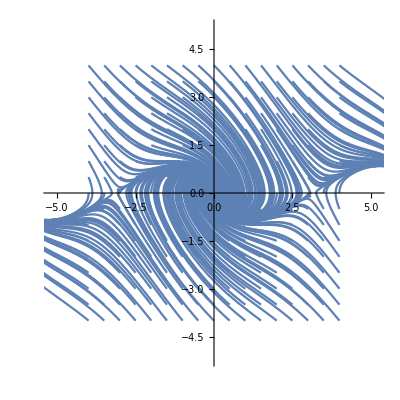

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol[initialC[[i,1]] , initialC[[i,2]]]]
,{t,0,5} , PlotRange->{{minx-0.5,maxx+0.5} , {miny-0.5,maxy+0.5}}],
{i,1,Length[initialC]}]/. Line[x_] :> {Arrowheads[{0.03,0.0}], Arrow[x]}
]
```